Piecewise[{{x/5, x<5}, {1, x≥5}, {0, True}}]

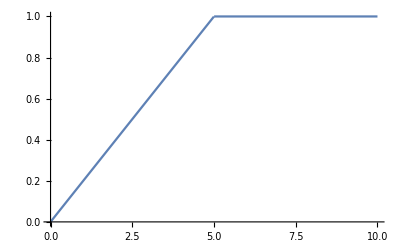

-Graphics-

```mathematica
myPw = Piecewise[{{x/5,x<5},{1,x≥ 5}}]
Plot[myPw,{x,0,10}]
Plot[myPw,{z,0,12}]
```

Note how if you define a function according to a variable, you must use that same variable name when using that function or Mathematica will think there’s no place for such input and will return a null.

Now it’s a simple matter to turn this into a surface of revolution

```mathematica
RevolutionPlot3D[myPw,{x,0,10}]
```

-Graphics3D-

Great!
Now let' s look at how to apply this to a function modeling a generic protrusion :

Piecewise[{{650-150 √(1-(150-z)^2/22500), 0<z≤150}, {500, 150<z≤4500}, {500 √(1-(-4500+z)^2/250000), 4500<z≤5000}, {0, True}}]

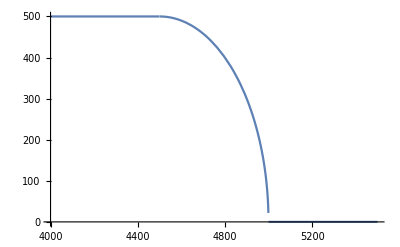

-Graphics3D-

```mathematica
R = 500;
rt = 150;
l = 5000;

pwR = Piecewise[{{R+rt-rt Cos[ArcSin[(rt-z)/rt]],0<z≤rt},{R,rt<z≤l-R},{(z-(l-R)) Tan[ArcCos[(z-(l-R))/R]],l-R<z≤ l}}]
Plot[pwR,{z,4000,l*1.1}]
RevolutionPlot3D[{pwR,z},{z,0,l}] 
	(*Note how we put pwR as "x" and put z last to make it the axis of revolution*)
```